# Модель процесса посадки на пневмоподушку

## Математические методы анализа и проектирования ракетно-космических систем

Юдинцев В. В.

Кафедра теоретической механики. Самарский университет

## Упрощенная модель

-Graphics-

Начальный периметр сечения баллона

```mathematica
Subscript[Π, 0]=π D0;
```

Деформированный периметр сечения баллона

```mathematica
Subscript[Π, x]=π (D0-x)+2s;
```

Из условия  сохранения периметра определим s

```mathematica
Solve[Subscript[Π, 0]==Subscript[Π, x],s]
```

{{s→(π x)/2}}

которое подставим в выражение для объема деформированного баллона

```mathematica
Subscript[V, x]=L((π (D0-x)^2)/4+s (D0-x))/. Solve[Subscript[Π, 0]==Subscript[Π, x],s][[1]]//FullSimplify
```

1/4 L π (D0-x) (D0+x)

При адиабатном процессе давление в баллоне будет определяться выражением

```mathematica
p0((Subscript[V, x]/.x->0)/Subscript[V, x])^k//FullSimplify
```

p0 (D0^2/(D0^2-x^2))^k

Создадим функцию давления

```mathematica
pbag[x_]:=Piecewise[{{p0(D0^2/(D0^2-x^2))^k,x>0},{p0,x<=0}}];
```

и силы действующей со стороны баллона на груз (с учетом давления среды)

```mathematica
Fbag[x_]:=Piecewise[{{π/2 x L(pbag[x]-pa),x>=0},{0,x<0}}];
```

При движении вверх (отскоке) при x < 0 сила не действует.

```mathematica
p={L->10.0,m->2000,g->9.81,u0->5,pa->0.10 10^6,D0->2.0,p0->0.10 10^6,k->1.4};
```

Уравнения движения груза

```mathematica
{m x''[t]==-Fbag[x[t]]+m g,x[0]==-1.5,x'[0]==u0}//.p
sol=NDSolve[%//.p,{x[t],x'[t],x''[t]},{t,0,5}][[1]];
```

{2000 x''[t]==19620.-(Piecewise[{{15.708 (-100000.+(Piecewise[{{696440. (1/(4.-x[t]^2))^1.4, x[t]>0}, {100000., x[t]≤0}, {0, True}}])) x[t], x[t]≥0}, {0, True}}]),x[0]==-1.5,x'[0]==5}

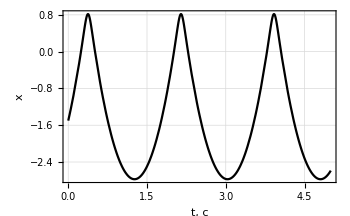

```mathematica
Plot[x[t]/.sol,{t,0,5},PlotRange->All,PlotTheme->{"Monochrome","FrameGrid"},FrameLabel->{"t, c","x"},ImageSize->350,PlotRange->All]
```

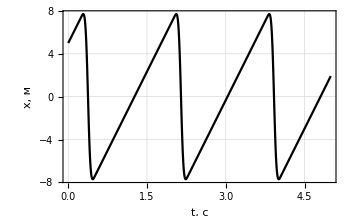

```mathematica
Plot[x'[t]/.sol,{t,0,5},PlotRange->All,PlotTheme->{"Monochrome","FrameGrid"},FrameLabel->{"t, c","x, м"},ImageSize->350]
```

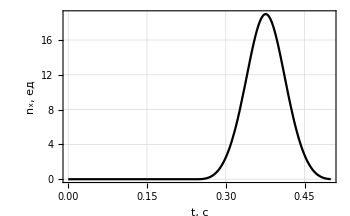

```mathematica
Plot[Fbag[x[t]]/(m g)/.sol//.p,{t,0,0.5},PlotRange->All,PlotTheme->{"Monochrome","FrameGrid"},FrameLabel->{"t, c","n_x, ед"},ImageSize->350]
```

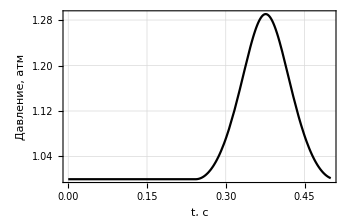

```mathematica
Plot[pbag[x[t]]/10^5/.sol//.p,{t,0,0.5},PlotRange->All,PlotTheme->{"Monochrome","FrameGrid"},FrameLabel->{"t, c","Давление, атм"},ImageSize->350]
```

### Анимация

```mathematica
baloon[x_]:=
Module[{d=Piecewise[{{D0-x,x>0},{D0,x<=0}}],s=Piecewise[{{π x/2,x>0},{0,x<=0}}]},
{
Darker[Green,0.3],
Rectangle[{-1,d/2},{1,d/2+1}],
Lighter[Blue,0.8],
Disk[{-s/2,0},d/2],
Disk[{+s/2,0},d/2],
Rectangle[{-s/2,-d/2},{s/2,d/2}]
}
];

getFrame[tt_]:=
Graphics[
Translate[baloon[x[t]],{0,-x[t]}]/.sol//.p/.t->tt,
PlotRange->{{-5,5},{-1.5,6}},Frame->True];

Animate[getFrame[tt],{tt,0,5}]
```

## Учитываем дренаж...

...

... модель в SimInTech

## Литература

Е. В. Герц, Г. В. Крейнин Расчёт пневмоприводов Справочное пособие М.: Машиностроение, 1975.

Zhou X., Zhou S. M., Li D. K. Optimal Design of Airbag Landing System without Rebound // IOP Conference Series: Materials Science and Engineering. 2019. № 1 (531). C. 012001.

Lei B. [и др.]. Dynamic modeling and simulation for pneumatic landing airbag system with frictional contact // Thin-Walled Structures. 2024. (195). C. 111417.

Shen X., Wang X., Liu C. A review of airbag landing system for spacecraft // Chinese Journal of Aeronautics. 2025. № 8 (38). C. 103569.

Saad M. A. Compressible fluid flow. под ред. T. Aloisi, Englewodd Cliffs, New Jersey: Prentice Hall, 1985.